# Pregunta 2 Tarea 4

```mathematica
gravityConstant=ℊ;
𝓇=leyMovimiento;
𝓋=leyVelocidad;
```

WolframAlphaQueryParseResults

9.8 m/s^2

```mathematica
L=2;(*m*)
ω=1.3;(*rad/s*)
ℊ=QuantityMagnitude[Quantity[9.8`3., ("Meters")/("Seconds")^2]];
```

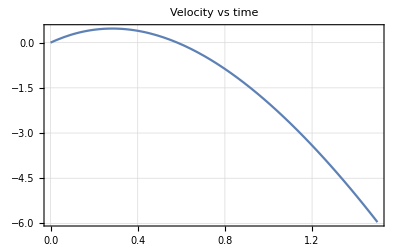

```mathematica
Plot[𝓋[t,L,ω],{t,0,1.5},
Frame->True,PlotRange->All,GridLines->Automatic,
PlotLabel->Style["Velocity vs time",16]
]
```

```mathematica
tmax=t/.FindRoot[𝓋[t,L,ω],{t,1}][[1]]
```

0.582214

### Posicion más distante:

```mathematica
Quantity[𝓇[tmax,L,ω],"Meters"]
```

2.18153 m

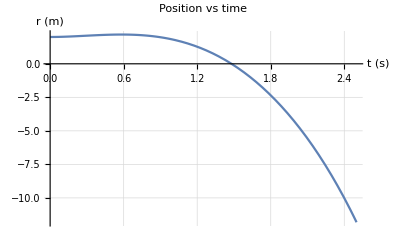

```mathematica
p1=Plot[𝓇[t,L,ω],{t,0,2.5},PlotRange->All,GridLines->Automatic,
PlotLabel->Style["Position vs time",16],AxesLabel->{Style["t (s)",12],Style["r (m)",12]}
]
```

### Punto inferior del plano

```mathematica
tr0=Quantity[t/.FindRoot[𝓇[t,L,ω],{t,2}][[1]],"Seconds"]
```

1.47973 s

Punto en el que la pelota despeja del plano inclinado es cuando θ = π/2 -> t = π/2 ω

```mathematica
tplano=Quantity[π/(2ω),"Seconds"]
```

1.2083 s

```mathematica
l1=Graphics[{Thick,Dashed,Line[{{𝓇[π/(2ω),L,ω],-13},{𝓇[π/(2ω),L,ω],3}}]}];
```

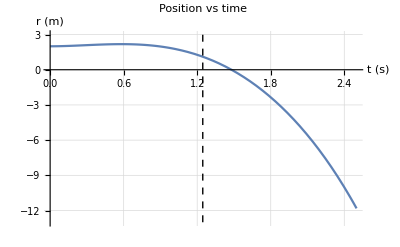

```mathematica
Show[p1,l1]
```

#### Del gráfico podemos observar que segundo el modelo planteado la particula deja el plano inclinado antes de llegar al origen o centro del plano . Segun el modelo la particula deja el plano en el segundo 1.2083 s pero llega al origen en 1.47973 s . El resultado que tiene sentido solo es el primero, el tiempo en que llega a una máxima distancia .